# NG^21 P_06. Метод опорных векторов: ядра и штрафы

Бельская Екатерина,
 5 группа, 2 курс

## 1. Ядро вместо расширенного фазового пространства

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Train=Import["NG21P05Problem.xlsx",{"Sheets","БельскаяЕ"}]⟦2;;4871⟧]
```

{4870,3}

```mathematica
X=Train⟦All,1;;2⟧;
```

```mathematica
Y=Train⟦All,3⟧;
```

```mathematica
Map[Dimensions,{iCold=First[#]&/@Position[Train,-1.],
iWarm=First[#]&/@Position[Train, 1.]}]
```

{{2396},{2474}}

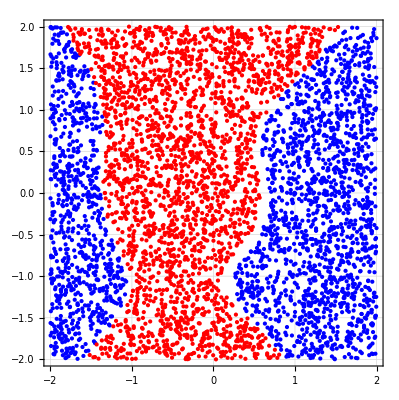

```mathematica
Fig0=Graphics[{Blue,Point@X⟦iCold⟧,Red, Point@X⟦iWarm⟧},Frame->True,GridLines->Automatic]
```

```mathematica
func=With[{$=Flatten@Table[#1^(d-k)#2^k,{d,4},{k,0,d}]},$&];
```

```mathematica
func1=Expand[(1+#1.#2)^4]&;
```

```mathematica
x={x1,x2};
y={y1,y2};
```

```mathematica
res1=(func@@x).(func@@y)
```

x1 y1+x1^2 y1^2+x1^3 y1^3+x1^4 y1^4+x2 y2+x1 x2 y1 y2+x1^2 x2 y1^2 y2+x1^3 x2 y1^3 y2+x2^2 y2^2+x1 x2^2 y1 y2^2+x1^2 x2^2 y1^2 y2^2+x2^3 y2^3+x1 x2^3 y1 y2^3+x2^4 y2^4

```mathematica
res2=func1@@{x,y}
```

1+4 x1 y1+6 x1^2 y1^2+4 x1^3 y1^3+x1^4 y1^4+4 x2 y2+12 x1 x2 y1 y2+12 x1^2 x2 y1^2 y2+4 x1^3 x2 y1^3 y2+6 x2^2 y2^2+12 x1 x2^2 y1 y2^2+6 x1^2 x2^2 y1^2 y2^2+4 x2^3 y2^3+4 x1 x2^3 y1 y2^3+x2^4 y2^4

Результаты различаются только коэффициентами

## 2. Оптимизация вычисления ядра

```mathematica
xD=X⟦1;;2000⟧;
yD=Y⟦1;;2000⟧;
```

```mathematica
Ker1=(1+#1.#2)^4&;
```

```mathematica
Ker2=Compile[{{x,_Real, 1},{y, _Real,1}},(1.+x.y)^4];
```

```mathematica
Ker3=Compile[{{x,_Real, 1},{y, _Real,1}},(1.+x.y)^4, Parallelization->True, RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"];
```

```mathematica
Ker1[X⟦1⟧,X⟦2⟧]
```

0.0826194

```mathematica
Ker2[X⟦1⟧,X⟦2⟧]
```

0.0826194

```mathematica
Ker3[X⟦1⟧,X⟦2⟧]
```

0.0826194

```mathematica
r1=Timing@Dimensions[Table[yD⟦r⟧*yD⟦c⟧*#[xD⟦r⟧,xD⟦c⟧],{r,1,Length@xD},{c,1,Length@xD}]]&/@{Ker1,Ker2,Ker3}
```

{{12.5156,{2000,2000}},{8.8125,{2000,2000}},{8.98438,{2000,2000}}}

```mathematica
r2=Timing@Dimensions[Array[yD⟦#1⟧*yD⟦#2⟧*#[xD⟦#1⟧,xD⟦#2⟧]&,{Length@xD,Length@xD},{1,1}]]&/@{Ker1,Ker2,Ker3}
```

{{10.3906,{2000,2000}},{10.2344,{2000,2000}},{10.2031,{2000,2000}}}

```mathematica
r3=Timing@Dimensions[Outer[yD⟦#1⟧*yD⟦#2⟧*#[xD⟦#1⟧,xD⟦#2⟧]&, Range[Length@xD], Range[Length@xD]]]&/@{Ker1,Ker2,Ker3}
```

{{11.9063,{2000,2000}},{10.375,{2000,2000}},{10.9531,{2000,2000}}}

```mathematica
r11=Timing@Dimensions[ParallelTable[yD⟦r⟧*yD⟦c⟧*#[xD⟦r⟧,xD⟦c⟧],{r,1,Length@xD},{c,1,Length@xD}]]&/@{Ker1,Ker2,Ker3}
```

{{1.42188,{2000,2000}},{0.796875,{2000,2000}},{0.828125,{2000,2000}}}

```mathematica
r12=Timing@Dimensions[ParallelArray[yD⟦#1⟧*yD⟦#2⟧*#[xD⟦#1⟧,xD⟦#2⟧]&,{Length@xD,Length@xD},{1,1}]]&/@{Ker1,Ker2,Ker3}
```

{{16.1094,{2000,2000}},{17.6406,{2000,2000}},{17.3125,{2000,2000}}}

```mathematica
r13=Timing@Dimensions@Parallelize[Outer[yD⟦#1⟧*yD⟦#2⟧*#[xD⟦#1⟧,xD⟦#2⟧]&, Range[Length@xD], Range[Length@xD]]]&/@{Ker1,Ker2,Ker3}
```

{{16.3594,{2000,2000}},{17.3281,{2000,2000}},{17.1719,{2000,2000}}}

```mathematica
Grid[{{"","Table","Array","Outer","ParallelTable","ParallelArray","ParallelOuter"},{"Function",r1⟦1,1⟧,r2⟦1,1⟧,r3⟦1,1⟧,r11⟦1,1⟧,r12⟦1,1⟧,r13⟦1,1⟧},
{"Compile",r1⟦2,1⟧,r2⟦2,1⟧,r3⟦2,1⟧,r11⟦2,1⟧,r12⟦2,1⟧,r13⟦2,1⟧},
{"Compile+",r1⟦3,1⟧,r2⟦3,1⟧,r3⟦3,1⟧,r11⟦3,1⟧,r12⟦3,1⟧,r13⟦3,1⟧}},
Frame->All]
```

| Table | Array | Outer | ParallelTable | ParallelArray | ParallelOuter
Function | 12.5156 | 10.3906 | 11.9063 | 1.42188 | 16.1094 | 16.3594
Compile | 8.8125 | 10.2344 | 10.375 | 0.796875 | 17.6406 | 17.3281
Compile+ | 8.98438 | 10.2031 | 10.9531 | 0.828125 | 17.3125 | 17.1719

Я брала 2000 точек. Почему - то получилось дольше всего в ParallelArray и Outer Parallelized, хотя в примере иначе

## 3. Радиально - базисная функция Гаусса в качестве ядра

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Dimensions[Train=Import["NG21P04Problem.xlsx",{"Sheets","БельскаяЕ"}]]
```

{3000,3}

```mathematica
X=Train⟦All,1;;2⟧;
```

```mathematica
Y=Train⟦All,3⟧;
```

```mathematica
Map[Dimensions,{iCold=First[#]&/@Position[Train,-1.],
iWarm=First[#]&/@Position[Train, 1.]}]
```

{{1840},{1160}}

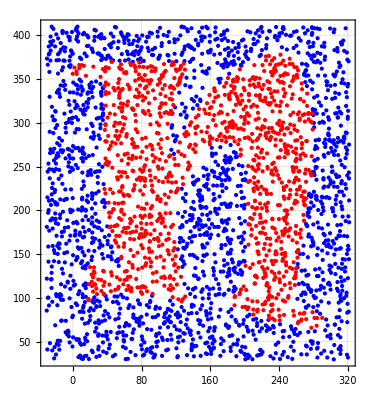

```mathematica
Fig0=Graphics[{Blue,Point@X⟦iCold⟧,Red, Point@X⟦iWarm⟧},Frame->True,GridLines->Automatic]
```

```mathematica
m=Mean[X]
```

{145.825,223.187}

```mathematica
s=Mean[StandardDeviation[X]]
```

105.343

```mathematica
K[x_,y_,σ_]:=Exp[(-(x-y).(x-y))/(2 σ^2)]
```

```mathematica
Plot3D[K[{x,y},m,s],{x,-40,320},{y,20,420},PlotRange->Full,ColorFunction->"GreenPinkTones"]
```

-Graphics3D-

```mathematica
ClearAll[W0];
W0[]:=Block[
{iSC = Join[iS,iC],ΛYsc=Join[λS Y⟦iS⟧,surCharge Y⟦iC⟧],Xsc=X⟦Join[iS,iC]⟧,size = Length[Join[iS,iC]]},
Median[
(ParallelSum[ΛYsc⟦s⟧*Ker[Xsc⟦s⟧,#],{s,size}]&/@Xsc)-Y⟦iSC⟧
]
];
```

```mathematica
ClearAll[SVM1];
SVM1[w0_]:=With[{ΛYsc=Join[λS Y⟦iS⟧,surCharge Y⟦iC⟧],Xsc=X⟦Join[iS,iC]⟧},Compile[{{x,_Real,1}},(Ker[#,x]&/@Xsc).ΛYsc-w0,Parallelization->True,RuntimeAttributes->{Listable},RuntimeOptions->"Speed",CompilationTarget->"C"]]
```

```mathematica
ClearAll[M];
M[i_]:=Y⟦i⟧SVM[X⟦i⟧];
SetAttributes[M,Listable];
```

```mathematica
ClearAll[Kerr];
Kerr[σ_]:=Compile[{{x,_Real, 1},{y,_Real, 1}},Exp[(-(x-y).(x-y))/(2 σ^2)], Parallelization->True, RuntimeAttributes->{Listable},
RuntimeOptions->"Speed"];
```

```mathematica
ClearAll[Figg];
Figg[]:=Show[Fig0,ContourPlot[SVM@{x1,x2},{x1,-40,320},{x2,20,420},Contours->{-1,0,1},ContourShading->{Hue[0.67,1,1,0.3],GrayLevel[0,0],GrayLevel[0,0],Hue[0,1,1,0.3]}],Graphics[  {Green, AbsoluteThickness@4,Circle[#,Offset@4]&/@X⟦iS⟧,Gray,Circle[#,Offset@4]&/@X⟦iC⟧}],PlotLabel->StringForm["Step=``,σ=``,C=``,iS=``,iC=``,iO=``",Step,σ,surCharge,Length@iS,Length@iC,Length@iO]]
```

## 4. Нарушители и штрафы

```mathematica
ClearAll[condition];
```

```mathematica
condition[]:=
(
Qss=ParallelArray[Y⟦iS⟦#1⟧⟧*Y⟦iS⟦#2⟧⟧*Ker[X⟦iS⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iS,Length@iS}];
Qcs=ParallelArray[Y⟦iC⟦#1⟧⟧*Y⟦iS⟦#2⟧⟧*Ker[X⟦iC⟦#1⟧⟧,X⟦iS⟦#2⟧⟧]&,{Length@iC,Length@iS}];
{1/2 Qss.λ.λ +If[Length@Qcs>0,surCharge*Total[Qcs.λ],0]-Total[λ],
Y⟦iS⟧.λ+surCharge*Total[Y⟦iC⟧]==0 && And@@(-surCharge≤ #&/@λ)})
```

```mathematica
ClearAll[SolveQP];
SolveQP[]:=(λ= ToExpression[StringJoin["λ",ToString[#]]&/@Range[Length[iS]]];λS=Values@Last@FindMinimum[condition[],λ]);
```

## 5. Инициализация множества опорных точек

```mathematica
ClearAll[kmSupport];InitSupport[]:=Module[{i=1,iSC, iSW,l},
iSC=First@RandomChoice[iCold,1];
iSW=First@Nearest[X⟦iWarm⟧->"Index",X⟦iSC⟧];
l={iSC, iSW};
While[True,If[i==1,iSC=First@Nearest[X⟦iCold⟧->"Index",X⟦iWarm⟧⟦iSW⟧];i--,iSW=First@Nearest[X⟦iWarm⟧->"Index",X⟦iCold⟧⟦iSC⟧];i++];l=Join[l,{iSC,iSW}];
If[l⟦-1⟧==l⟦-3⟧ && l⟦-2⟧==l⟦-4⟧,Break[],Continue[]]];
Flatten[Position[X,#]&/@{X⟦iCold⟧⟦iSC⟧,X⟦iWarm⟧⟦iSW⟧}]]
```

```mathematica
InitSupport[counter_]:=Module[{iS={}},Do[iS=Union[iS,InitSupport[]],counter];iS]
```

## 6. Неразделимые классы

```mathematica
ClearAll[TrainSVM];TrainSVM[Sigma_,C_,counter_]:=Monitor[
σ=Sigma;
surCharge=C;Fig=Fig0;
Ker=Kerr[Sigma];
iS=InitSupport[counter];
iC={};
iO=Complement[Range[Length@X],iS,iC];
λ=ToExpression[StringJoin["λ",ToString[#]]&/@Range[Length[iS]]];
Step=0;ind=1;

While[ind≠0,Switch[ind,
1,SolveQP[];SVM=SVM1[W0[]];
Step++;
ind=2;
Fig=Figg[],

2,ind=If[(iBad=Flatten@Position[λS,i_/;i<=0])=={},3,iBad=RandomChoice[Abs@λS⟦iBad⟧->iBad];
AppendTo[iO,iS⟦iBad⟧];
iS=Delete[iS,iBad];
1],

3,ind=If[(iBad=Flatten@Position[λS,i_/;i≥ surCharge])=={},4,iBad=RandomChoice[(λS⟦iBad⟧-surCharge)->iBad];
AppendTo[iC,iS⟦iBad⟧];
iS=Delete[iS,iBad];
1],

4,ind=If[margins=M[iO];(iBad=Flatten@Position[margins,i_/;i≤1])=={},5,
iBad=RandomChoice[Abs[1-margins⟦iBad⟧]->iBad];
AppendTo[iS,iO⟦iBad⟧];
iO=Delete[iO,iBad];
1],

5,ind=If[margins=M[iC];(iBad=Flatten@Position[margins,i_/;i≥ 1])=={},0,
iBad=RandomChoice[Abs[1-margins⟦iBad⟧]->iBad];
AppendTo[iS,iC⟦iBad⟧];
iC=Delete[iC,iBad];
1]
]];Fig,Fig];
```

```mathematica
TrainSVM[105,100000,10]
```

```mathematica
s=Mean[StandardDeviation[X]]
```

105.343

С такими начальными данными получилось много точек - нарушителей. Кроме того, оно очень долго считало, поэтому я остановила подсчет (на картинке 3454 ый шаг)